```mathematica
Needs["NVSim`"]
```

### Overview

The main function of NVSim is EvalPulse[H,p], where H is the Hamiltonian, and p is the pulse. By pulse, we mean one of three things:

(1)  A drift pulse: the evolution under the Hamiltonian for some time. In this case, p is just equal to a number

(2)  An instantaneous pulse: the Hamiltonian is ignored and some other unitary is applied. This kind of pulse only really makes within pulse sequences. In this case, p is of the form {U,t} where U is the unitary matrix and t is how much time the pulse should take.

(3)   A shaped pulse: A list of control Hamiltonians, time spacings, and amplitudes is provided, and everything is simulated. In this case, p is of the form {pulse,{Hctl1,Hctl2,...}} where pulse is either a text file (eg. CVS) containing the pulse, or the pulse itself. A pulse is of the form {dt1,a11,a12,a13,...},{dt2,a21,a22,a23,...},{dt2,a21,a22,a23,...},...}.

The Hamiltonian H can be either time dependent, in which case it is just a matrix, or time dependent, in which case it is a function taking one real argument, and returning a matrix. For example:

```mathematica
TimeDepHam=3Z;
TimeIndepHam[t_]=Cos[t]Z;
```

In addition to the inputs H and p, there are also several options. Instead of explicitly listing them all and what they do, for this would be tedious, I will trust that you can garner their meanings from the examples which follow. I will mention, however, that you can view all the options by typing:

```mathematica
Options[SimulationOptions]
```

{StepSize→Automatic,PollingInterval→Off,InitialState→None,Observables→None,Functions→None,SimulationOutput→Automatic,SequenceMode→False}

And moreover, that using the ? symbol will yeild quick descriptions:

```mathematica
?StepSize
```

StepSize is a simulation option that chooses the time discretization when the internal Hamiltonian is time dependent. Can be set to Automatic.

### Simplest Example

We evolve under X/2 for a time π:

```mathematica
EvalPulse[X/2,π]
```

{{Unitaries,{{{1,0},{0,1}},{{0,-ⅈ},{-ⅈ,0}}}},{TimeVector,{0,π}}}

The TimeVector shows the times at which an output is returned. Since we have not entered an initial state, the output defaults to displaying the unitaries at these times. In this simple example we see that at time 0, we have the identity unitary, and at time π, we have e^(-I π X/2).

### Next Simplest Examples: Using Options

#### InitialState

If we enter an initial state, the output automatically chooses to track this state over time:

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0]
```

{{States,{{{1,0},{0,0}},{{0,0},{0,1}}}},{TimeVector,{0,π}}}

Now we know the state of the system at all times in the TimeVector.

#### PollingInterval

We may want to know things about the system at intermedate times. This is done through PollingInterval.

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3]
```

{{States,{{{1,0},{0,0}},{{0.977668+0. ⅈ,0.+0.14776 ⅈ},{0.-0.14776 ⅈ,0.0223318+0. ⅈ}},{{0.912668+0. ⅈ,0.+0.282321 ⅈ},{0.-0.282321 ⅈ,0.0873322+0. ⅈ}},{{0.810805+0. ⅈ,0.+0.391663 ⅈ},{0.-0.391663 ⅈ,0.189195+0. ⅈ}},{{0.681179+0. ⅈ,0.+0.46602 ⅈ},{0.-0.46602 ⅈ,0.318821+0. ⅈ}},{{0.535369+0. ⅈ,0.+0.498747 ⅈ},{0.-0.498747 ⅈ,0.464631+0. ⅈ}},{{0.386399+0. ⅈ,0.+0.486924 ⅈ},{0.-0.486924 ⅈ,0.613601+0. ⅈ}},{{0.247577+0. ⅈ,0.+0.431605 ⅈ},{0.-0.431605 ⅈ,0.752423+0. ⅈ}},{{0.131303+0. ⅈ,0.+0.337732 ⅈ},{0.-0.337732 ⅈ,0.868697+0. ⅈ}},{{0.0479639+0. ⅈ,0.+0.21369 ⅈ},{0.-0.21369 ⅈ,0.952036+0. ⅈ}},{{0.00500375+0. ⅈ,0.+0.07056 ⅈ},{0.-0.07056 ⅈ,0.994996+0. ⅈ}},{{1.61971×10^-31+0. ⅈ,0.-4.02456×10^-16 ⅈ},{0.+4.02456×10^-16 ⅈ,1.+0. ⅈ}}}},{TimeVector,{0,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,π}}}

Now we know the state of the system every 0.3 units of time. Notice that PollingInterval does not have to evenly divide the total evolution time. This is in general true, PollingInterval need have no relation to any time scale in your problem.

#### Observables

You may want to track the expectation values of some observables. This can be done through Observables:

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{Z}]
```

{{Observables,{{1},{0.955336},{0.825336},{0.62161},{0.362358},{0.0707372},{-0.227202},{-0.504846},{-0.737394},{-0.904072},{-0.989992},{-1.}}},{TimeVector,{0,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,π}}}

Note that Observables must be a list even if we are only interested in only one observable. We can also track multiple observables:

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}]
```

{{Observables,{{0,0,1},{0.,-0.29552,0.955336},{0.,-0.564642,0.825336},{0.,-0.783327,0.62161},{0.,-0.932039,0.362358},{0.,-0.997495,0.0707372},{0.,-0.973848,-0.227202},{0.,-0.863209,-0.504846},{0.,-0.675463,-0.737394},{0.,-0.42738,-0.904072},{0.,-0.14112,-0.989992},{0.,8.04912×10^-16,-1.}}},{TimeVector,{0,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,π}}}

#### Functions

You may want to track the evolution of some arbitrary function(s), like the purity of a subsystem. This can be done through Functions, which is similar in flavour to Observables.

```mathematica
ρ0=Projector[{0,1,0,0}];
f[ρ_]:=Purity[PartialTr[ρ,{2,2},{2}]];
EvalPulse[𝟙⊗Z+Z⊗𝟙+X⊗X+Y⊗Y+Z⊗Z,10π,PollingInterval->1,InitialState->ρ0,Functions->{f}]//Chop
```

{{Functions,{{1},{0.713625},{0.510585},{0.856045},{0.958556},{0.583265},{0.589964},{0.963305},{0.847964},{0.508187},{0.722403},{0.999843},{0.704892},{0.513283},{0.863992},{0.953545},{0.576776},{0.596863},{0.967787},{0.839761},{0.506093},{0.731216},{0.999373},{0.696216},{0.516278},{0.871797},{0.94828},{0.570504},{0.603954},{0.971996},{0.831445},{0.504304},{1.}}},{TimeVector,{0,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,10 π}}}

Next we ask for both some observables and functions:

```mathematica
ρ0=Projector[{0,1,0,0}];
f[ρ_]:=Purity[PartialTr[ρ,{2,2},{2}]];
EvalPulse[𝟙⊗Z+Z⊗𝟙+X⊗X+Y⊗Y+Z⊗Z,10π,PollingInterval->1,InitialState->ρ0,Functions->{f},Observables->{Z⊗𝟙}]//Chop
```

{{Observables,{{1},{-0.653644},{-0.1455},{0.843854},{-0.957659},{0.408082},{0.424179},{-0.962606},{0.834223},{-0.127964},{-0.666938},{0.999843},{-0.640144},{-0.162991},{0.85322},{-0.952413},{0.391857},{0.440143},{-0.967251},{0.824331},{-0.110387},{-0.680023},{0.999373},{-0.626444},{-0.18043},{0.862319},{-0.946868},{0.37551},{0.455969},{-0.971592},{0.814181},{-0.0927762},{1.}}},{Functions,{{1},{0.713625},{0.510585},{0.856045},{0.958556},{0.583265},{0.589964},{0.963305},{0.847964},{0.508187},{0.722403},{0.999843},{0.704892},{0.513283},{0.863992},{0.953545},{0.576776},{0.596863},{0.967787},{0.839761},{0.506093},{0.731216},{0.999373},{0.696216},{0.516278},{0.871797},{0.94828},{0.570504},{0.603954},{0.971996},{0.831445},{0.504304},{1.}}},{TimeVector,{0,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,10 π}}}

Functions do not have to return numbers; they can return anything you want. For example you can return subsystems:

```mathematica
f[ρ_]:=PartialTr[ρ,{2,2},{1}]
```

#### Customizing the output

You may have noticed that the output of the EvalPulse was chosen automatically for you in the previous examples. Suppose that you want something other than what it’s giving you, e.g. you want both the States and the Observables. You can use SimulationOutput to acheive this.

```mathematica
ρ0={{1,0},{0,0}};
EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{Z},SimulationOutput->{States,Observables}]
```

{{States,{{{1,0},{0,0}},{{0.977668+0. ⅈ,0.+0.14776 ⅈ},{0.-0.14776 ⅈ,0.0223318+0. ⅈ}},{{0.912668+0. ⅈ,0.+0.282321 ⅈ},{0.-0.282321 ⅈ,0.0873322+0. ⅈ}},{{0.810805+0. ⅈ,0.+0.391663 ⅈ},{0.-0.391663 ⅈ,0.189195+0. ⅈ}},{{0.681179+0. ⅈ,0.+0.46602 ⅈ},{0.-0.46602 ⅈ,0.318821+0. ⅈ}},{{0.535369+0. ⅈ,0.+0.498747 ⅈ},{0.-0.498747 ⅈ,0.464631+0. ⅈ}},{{0.386399+0. ⅈ,0.+0.486924 ⅈ},{0.-0.486924 ⅈ,0.613601+0. ⅈ}},{{0.247577+0. ⅈ,0.+0.431605 ⅈ},{0.-0.431605 ⅈ,0.752423+0. ⅈ}},{{0.131303+0. ⅈ,0.+0.337732 ⅈ},{0.-0.337732 ⅈ,0.868697+0. ⅈ}},{{0.0479639+0. ⅈ,0.+0.21369 ⅈ},{0.-0.21369 ⅈ,0.952036+0. ⅈ}},{{0.00500375+0. ⅈ,0.+0.07056 ⅈ},{0.-0.07056 ⅈ,0.994996+0. ⅈ}},{{1.61971×10^-31+0. ⅈ,0.-4.02456×10^-16 ⅈ},{0.+4.02456×10^-16 ⅈ,1.+0. ⅈ}}}},{Observables,{{1},{0.955336},{0.825336},{0.62161},{0.362358},{0.0707372},{-0.227202},{-0.504846},{-0.737394},{-0.904072},{-0.989992},{-1.}}},{TimeVector,{0,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,π}}}

### Methods for formatting the output with applications toward plotting

The functions TimeVector, Unitaries, States, Observables, and Functions, in addition to serving as placeholders as seen in the previous section, can be used to format the output.

#### TimeVector

TimeVector simply extracts the TimeVector:

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π]
TimeVector[data]
```

{{Unitaries,{{{1,0},{0,1}},{{0,-ⅈ},{-ⅈ,0}}}},{TimeVector,{0,π}}}

{0,π}

#### Unitaries

Unitaries simply extracts the Unitaries:

```mathematica
data=EvalPulse[X/2,π]
Unitaries[data]
```

{{Unitaries,{{{1,0},{0,1}},{{0,-ⅈ},{-ⅈ,0}}}},{TimeVector,{0,π}}}

{{{1,0},{0,1}},{{0,-ⅈ},{-ⅈ,0}}}

Unitaries[data,t] extracts the unitary from the list Unitaries[data] whose time lies closest to t:

```mathematica
data=EvalPulse[X/2,π]
Unitaries[data,π/8]
Unitaries[data,3π/4]
```

{{Unitaries,{{{1,0},{0,1}},{{0,-ⅈ},{-ⅈ,0}}}},{TimeVector,{0,π}}}

{{1,0},{0,1}}

{{0,-ⅈ},{-ⅈ,0}}

#### States

States functions identically to Unitaries. States simply extracts the States:

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0]
States[data]
```

{{States,{{{1,0},{0,0}},{{0,0},{0,1}}}},{TimeVector,{0,π}}}

{{{1,0},{0,0}},{{0,0},{0,1}}}

States[data,t] extracts the states from the list States[data] whose time lies closest to t:

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0]
States[data,π/8]
States[data,3π/4]
```

{{States,{{{1,0},{0,0}},{{0,0},{0,1}}}},{TimeVector,{0,π}}}

{{1,0},{0,0}}

{{0,0},{0,1}}

#### Observables

Observables[data] extracts the observables from data and transposes them. The transposing feature is useful for ListPlot

{{Observables,{{0,0,1},{0.,-0.29552,0.955336},{0.,-0.564642,0.825336},{0.,-0.783327,0.62161},{0.,-0.932039,0.362358},{0.,-0.997495,0.0707372},{0.,-0.973848,-0.227202},{0.,-0.863209,-0.504846},{0.,-0.675463,-0.737394},{0.,-0.42738,-0.904072},{0.,-0.14112,-0.989992},{0.,8.04912×10^-16,-1.}}},{TimeVector,{0,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,π}}}

{{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0,-0.29552,-0.564642,-0.783327,-0.932039,-0.997495,-0.973848,-0.863209,-0.675463,-0.42738,-0.14112,8.04912×10^-16},{1,0.955336,0.825336,0.62161,0.362358,0.0707372,-0.227202,-0.504846,-0.737394,-0.904072,-0.989992,-1.}}

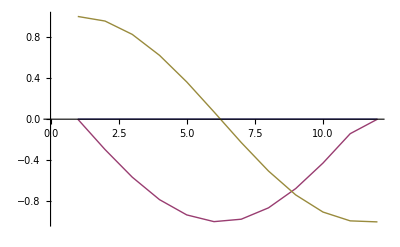

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}]
Observables[data]
ListPlot[Observables[data],Joined->True]
```

Observables has an option TimeVector which you can set to true to include time coordinates along with the observables:

{{{0,0},{0.3,0.},{0.6,0.},{0.9,0.},{1.2,0.},{1.5,0.},{1.8,0.},{2.1,0.},{2.4,0.},{2.7,0.},{3.,0.},{π,0.}},{{0,0},{0.3,-0.29552},{0.6,-0.564642},{0.9,-0.783327},{1.2,-0.932039},{1.5,-0.997495},{1.8,-0.973848},{2.1,-0.863209},{2.4,-0.675463},{2.7,-0.42738},{3.,-0.14112},{π,8.04912×10^-16}},{{0,1},{0.3,0.955336},{0.6,0.825336},{0.9,0.62161},{1.2,0.362358},{1.5,0.0707372},{1.8,-0.227202},{2.1,-0.504846},{2.4,-0.737394},{2.7,-0.904072},{3.,-0.989992},{π,-1.}}}

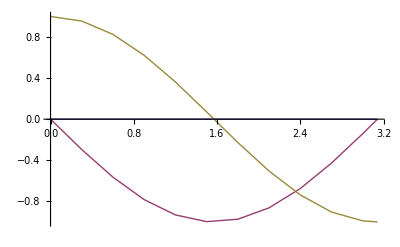

```mathematica
ρ0={{1,0},{0,0}};
data=EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}];
Observables[data,TimeVector->True]
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

Observables[data,n] extracts only the data from the n’th observable:

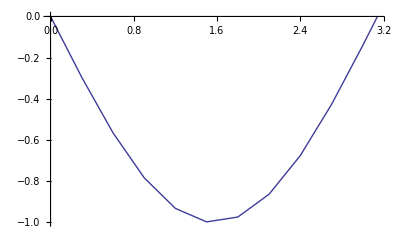

```mathematica
ρ0={{1,0},{0,0}};
ListPlot[Observables[EvalPulse[X/2,π,InitialState->ρ0,PollingInterval->0.3,Observables->{X,Y,Z}],2,TimeVector->True],Joined->True]
```

#### Functions

Functions[data] and Functions[data,n] behave identically to Observables; see the previous subsection.

### Time Dependence

#### First Example

The Hamiltonian H can be either time dependent, in which case it is just a matrix, or time dependent, in which case it is a function taking one real argument, and returning a matrix. In the previous sections we saw many time dependent examples. Here is a time dependent example with a DriftPulse:

{{Observables,{{1},{0.99995},{0.999205},{0.99601},{0.987553},{0.970153},{0.939553},{0.891336},{0.821455},{0.726834},{0.605996},{0.45959},{0.290721},{0.10499},{-0.08984},{-0.284518},{-0.469267},{-0.634865},{-0.773681},{-0.880486},{-0.952906},{-0.991478},{-0.999325},{-0.981558},{-0.944528},{-0.895075},{-0.839881},{-0.784976},{-0.735446},{-0.695295},{-0.667425},{-0.653692},{-0.654963},{-0.67116},{-0.701253},{-0.743214},{-0.793958},{-0.849295},{-0.903968},{-0.95181},{-0.986076},{-0.999956},{-0.987255},{-0.943145},{-0.864904},{-0.75247},{-0.608712},{-0.439305},{-0.252213},{-0.0568264},{0.13709},{0.13709}}},{TimeVector,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5}}}

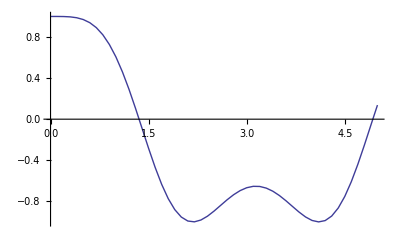

```mathematica
H[t_]=Sin[t]X;
data=EvalPulse[H,5,PollingInterval->0.1,InitialState->Projector[{1,0}],Observables->{Z}]
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

#### Controlling the StepSize

NVSim simulates time dependence by discretizing the time domain and assuming the Hamiltonian is constantly equal to the Hamiltonian at the midpoint on each of these small intervals. If no StepSize is given, one is automatically calculated by taking a tenth of the inverse of the norm of the Hamiltonian, minimized over all time. This may work, but in some cases this fails (eg your Hamiltonian is unbounded over time, eg H=t^2 X), and in some cases a value that is too small or too large is chosen. In these latter cases you will want to choose the value yourself:

{{Observables,{{1},{0.99995},{0.9998},{0.999551},{0.999201},{0.998752},{0.998204},{0.997555},{0.996807},{0.995959},{0.995012},{0.993966},{0.992821},{0.991576},{0.990232},{0.98879},{0.987248},{0.985609},{0.98387},{0.982034},{0.980099},{0.978067},{0.975937},{0.97371},{0.971385},{0.968964},{0.966445},{0.963831},{0.96112},{0.958313},{0.95541},{0.952412},{0.949319},{0.946131},{0.942849},{0.939472},{0.936002},{0.932438},{0.928781},{0.925032},{0.92119},{0.917256},{0.913231},{0.909114},{0.904907},{0.900609},{0.896222},{0.891745},{0.887179},{0.882524},{0.877781},{0.872024}}},{TimeVector,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5}}}

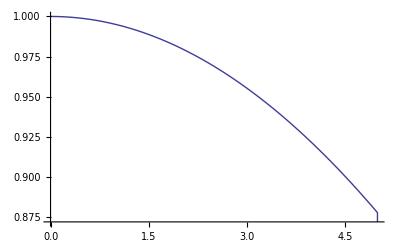

```mathematica
H[t_]=Sin[t]X;
data=EvalPulse[H,5,PollingInterval->0.1,InitialState->Projector[{1,0}],Observables->{Z},StepSize->0.01]
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

We see that the automatic value from the previous section was too large: those waves in the signal were ficticious.

You can check the value that would be chosen automatically with GetStepSize:

```mathematica
H[t_]=Sin[t]X;
GetStepSize[H]
```

0.1

To be clear: the StepSize and the PollingInterval are completely different and unrelated numbers. As an illustration, increasing the StepSize will decrease the accuracy of the simulation, whereas increasing the PollingInterval will simply course grain your plots.

### Shaped Pulses

The pulse shape can be specified either in a Mathematica matrix, or as a path to an external text file.

#### Example with matrix

In this example we use two control Hamiltonians, and only a handful of steps. The first element in each row of the shape matrix is the time of that step, and the rest are the amplitudes of the same step.

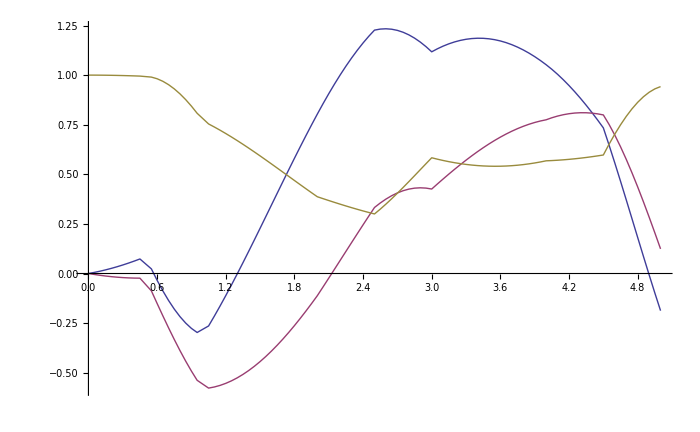

```mathematica
shape={{0.5,.1,.2},{0.5,1.4,0},{1.,.3,.4},{0.5,.1,.2},{0.5,1.4,0},{1.,.3,.4},{0.5,.1,.2},{0.5,1.4,0}};
Hctl1=X/2;
Hctl2=Y/2;
data=EvalPulse[
Z/2,
{shape,{Hctl1,Hctl2}},
PollingInterval->.05,
InitialState->Projector[{1,0}],
Observables->{X+Y,Y,Z}
];
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

#### Example with file

Every line of the file should be separated by some delimeter (comma, tab, I’m not sure what else woud work). The first column contains the time steps, the second to last column contain the amplitudes. Mathematica is pretty clever when importing files, so you can use scientific notation (0.5e-9) and stuff.

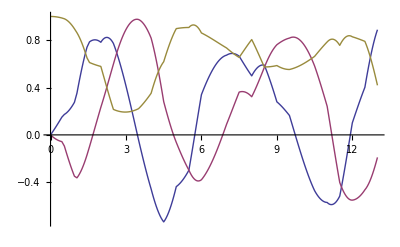

```mathematica
SetDirectory[NotebookDirectory[]];
Hctl1=X/2;
Hctl2=Y/2;
data=EvalPulse[
Z/2,
{"shape.csv",{Hctl1,Hctl2}},
PollingInterval->.05,
InitialState->Projector[{1,0}],
Observables->{X,Y,Z}
];
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

You can import the file to the matrix form as used in the previous subsection with GetPulseShapeMatrix:

```mathematica
SetDirectory[NotebookDirectory[]];
GetPulseShapeMatrix["shape.csv"]
```

{{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.},{1.,0.1,0.2},{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.},{1.,0.1,0.2},{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.},{1.,0.1,0.2},{0.5,0.2,0.3},{0.5,0.9,0.03},{0.5,0.1,0.9},{0.5,0.1,0.1},{0.5,0.2,1.}}

### Pulse Sequences

Pulse sequences can be simulated using the EvalPulseSequence[H,{p1,p2,p3,...}] function. This function does little more than evaluate EvalPulse[H,p1], EvalPulse[H,p2], etc. back to back. The “little more” it does do is very convenient: it ties the end result of the previous pulse into the initial conditions of the current pulse. For example, on the first pulse it will take InitialState as the initial state, but on subsequent pulses it will take the end state of the previous pulse as the initial state.

#### Example

Let’s just perform some random collection of pulses.

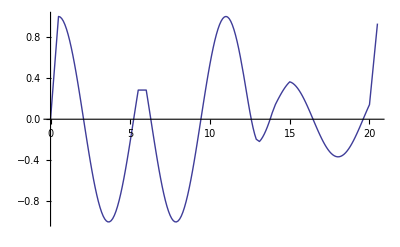

```mathematica
p1={(X+Z)/Sqrt[2],0.5};
p2=5;
p3={X,0.5};
p4=5;
p5={{{1,.1,.2},{1,1.4,0},{1.,.3,.4},{1,.1,.2}},{X/2,Y/2}};
p6=5;
p7=p1;
data=EvalPulseSequence[Z/2,{p1,p2,p3,p4,p5,p6,p7},InitialState->Projector[{1,0}],Observables->{X},PollingInterval->0.1];
ListPlot[Observables[data,TimeVector->True],Joined->True]
```

#### Drawing pulse sequences

This feature still needs some work, but, for example:

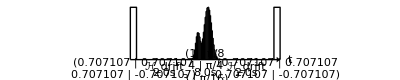

```mathematica
shapedpulse={{{1,π/8},{4,π/4},{3,π/16}},{X/2}};
seq={{(X+Z)/Sqrt[2],.1},2,shapedpulse,2,{(X+Z)/Sqrt[2],.1}};
DrawSequence[seq]
```

### Tips, Tricks and Troubleshooting

#### EvalPulse/EvalPulseSequence not evaluating6

Sometimes something won’t evaluate at all:

```mathematica
p1={(X+Z)/Sqrt[2],0.5};
p2=5;
p3=X;
p4=5;
p5={{{1,.1,.2},{1,1.4,0},{1.,.3,.4},{1,.1,.2}},{X/2,Y/2}};
p6=5;
p7=p1;
EvalPulseSequence[Z/2,{p1,p2,p3,p4,p5,p6,p7},InitialState->Projector[{1,0}],Observables->{X},PollingInterval->0.1]
```

EvalPulseSequence[{{1/2,0},{0,-1/2}},{{{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},0.5},5,{{0,1},{1,0}},5,{{{1,0.1,0.2},{1,1.4,0},{1.,0.3,0.4},{1,0.1,0.2}},{{{0,1/2},{1/2,0}},{{0,-ⅈ/2},{ⅈ/2,0}}}},5,{{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}},0.5}},InitialState→{{1,0},{0,0}},Observables→{{{0,1},{1,0}}},PollingInterval→0.1]

This is often caused by inputs in the wrong format. You can use PulseQ to test which of the pulses are valid:

```mathematica
PulseQ/@{p1,p2,p3,p4,p5,p6,p7}
```

{True,True,False,True,True,True,True}

We see that we forgot to include the time of the instantaneous pulse p3.

#### Simulating ranges of parameters

Simulating ranges of parameters is not builtin, but you can get around this with not too much effort. Suppose we want to simulate a Ramsey experiment (π/2 - τ - π/2: now vary τ and take the FT).

```mathematica
rot={MatrixExp[-I π/4(Sx+Sxp)/Sqrt[2]]⊗𝟙//N,1 10^-8};
Ham[t_]=Simplify[With[{Hint= 10^-6 NVHamiltonian[]⊗𝟙},MatrixExp[I t Hint].(10^-6 NVHamiltonian["nitrogenIsotope"->14,"B"->{10,0,0}]-Hint).MatrixExp[-I t Hint]]];
ρ0=Projector[{0,1,0}]⊗𝟙/3;
```

Warning: this will take like 20 minutes to run.

```mathematica
data=Table[
{
τ,
Last@Last@Observables@EvalPulseSequence[
Ham,
{rot,τ,rot},
StepSize->0.3 10^-3,
InitialState->ρ0,
Observables->{Projector[{0,1,0}]⊗𝟙}
]
},
{τ,.01,10,.01}
];
```

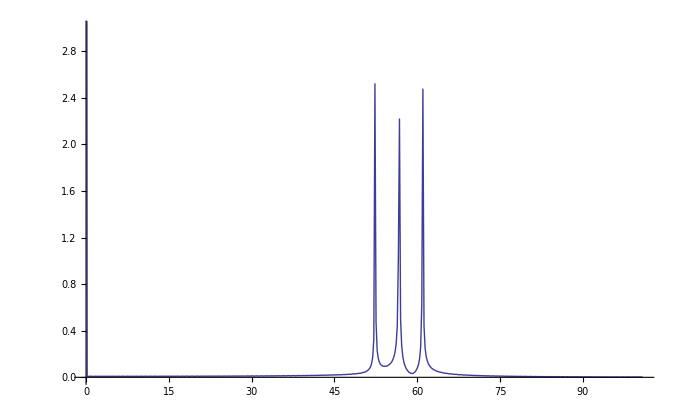

```mathematica
DiscreteFourierPlot[data[[All,2]],{0.05,5},{Abs},Joined->True,PlotRange->{0,3}]
```